# Some fun with differential equations

Let’s consider the following equation, and how to solve it as a series expansion using Mathematica,
	P(x)(d^2 y(x))/dx^2 + Q(x)(dy(x))/dx+R(x)y(x)=0,
for some P, Q, R, let’s say
	P(x)=x^2,
Q(x)=0,
R(x)=cos(x),
just to give some example. And for the boundary conditions,
	y(0)=1,
	y’(0)=0.

## Defining the problem

First, let’s define the equations, to define a function of some input argument:
- Square brackets around the argument
- Use an underscore after the argument
- “:=” is for defining a function which only evaluates when called whereas “=” is for assigning a value at the time of the definition.
I’ve done one definition below, you can fill out the others.

```mathematica
ClearAll[P,Q,R]
P[x_]:=(1+x^2)
Q[x_]:=0
R[x_]:=Cos[x]
```

Hopefully the following explains what is going on with the different assignments.

```mathematica
z=1;
testEquals[z_]=z^2
testColonEquals[z_]:=z^2;
```

1

```mathematica
testEquals[2]
testColonEquals[2]
```

1

4

In case we want to use the letter z below, we will clear the value that we have assigned to it.

```mathematica
ClearAll[z]
```

## Seeing if Mathematica knows the answer

Mathematica knows lots of differential equations, so sometimes it just knows the answer.

### Chebyshev equation

Below I show that it knows the answer to the Chebyshev equation (with α=1), though it might express them in a funny way. To test this we use “DSolve”. Hover over it and click to see the documentation. Note the use of “==” here, which is not assignment but mathematical equality.

```mathematica
ySolutions=DSolve[
(1-x^2)y''[x]-x y'[x]+y[x]==0,
y[x],
x
]
```

{{y[x]→C[1] Cosh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-ⅈ C[2] Sinh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]}}

Curly brackets here mean a list. That there are two layers means we have a list of a list, though only of length 1. To get an element of a list, use double square brackets. Note also that Mathematica starts counting from 1, not 0.

```mathematica
{the,cat,in,the,hat}[[2]]
```

cat

There is some more notation here in the solution above. The arrow is a kind of find and replace. To utilise it, use the notation “\.” as follows.

```mathematica
ySolution[x_]=y[x]/.ySolutions[[1]]
```

C[1] Cosh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-ⅈ C[2] Sinh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]

Let’s test that this really is a solution, by putting the solution back into the equation. Note that I am defining a variable with [1] after it. This is useful if I want to manipulate the object and define further versions of it below.

```mathematica
shouldBeZero[1]=((1-x^2)y''[x]-x y'[x]+y[x])/.ySolutions[[1]]
```

C[1] Cosh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-ⅈ C[2] Sinh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-x y'[x]+(1-x^2) y''[x]

That didn’t work! Why not? When something doesn’t work in Mathematica, a good trick is to see either the InputForm (or the FullForm) of the output.

```mathematica
InputForm[shouldBeZero[1]]
```

C[1]*Cosh[(2*Sqrt[1 - x^2]*ArcTan[Sqrt[1 - x^2]/(1 + x)])/Sqrt[-1 + x^2]] - I*C[2]*Sinh[(2*Sqrt[1 - x^2]*ArcTan[Sqrt[1 - x^2]/(1 + x)])/Sqrt[-1 + x^2]] - x*Derivative[1][y][x] + 
 (1 - x^2)*Derivative[2][y][x]

```mathematica
InputForm[ySolutions[[1]]]
```

{y[x] -> C[1]*Cosh[(2*Sqrt[1 - x^2]*ArcTan[Sqrt[1 - x^2]/(1 + x)])/Sqrt[-1 + x^2]] - I*C[2]*Sinh[(2*Sqrt[1 - x^2]*ArcTan[Sqrt[1 - x^2]/(1 + x)])/Sqrt[-1 + x^2]]}

You can see that while y[x] was replace, Derivative[1][y][x] wasn’t. Mathematica isn’t smart like this. The find and replace methods will only replace exact matches.

```mathematica
shouldBeZero[2]=shouldBeZero[1]/.{y'[x]->D[ySolution[x],x],y''[x]->D[ySolution[x],x,x]}
```

C[1] Cosh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-ⅈ C[2] Sinh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-x (-ⅈ ((2 √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2))-(2 x √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(3/2))-(2 x ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) √(-1+x^2))) C[2] Cosh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]+((2 √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2))-(2 x √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(3/2))-(2 x ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) √(-1+x^2))) C[1] Sinh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))])+(1-x^2) (((2 √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2))-(2 x √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(3/2))-(2 x ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) √(-1+x^2)))^2 C[1] Cosh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-ⅈ (-(2 √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2) (-(2 x)/(1+x)^2-(2 (1-x^2))/(1+x)^3))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2)^2)+(2 √(1-x^2) (-x^2/((1+x) (1-x^2)^(3/2))+(2 x)/((1+x)^2 √(1-x^2))-1/((1+x) √(1-x^2))+(2 √(1-x^2))/(1+x)^3))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2))-(4 x √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/((-1+x^2)^(3/2) (1+(1-x^2)/(1+x)^2))-(4 x (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/(√(1-x^2) √(-1+x^2) (1+(1-x^2)/(1+x)^2))+(6 x^2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(5/2))+(4 x^2 ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) (-1+x^2)^(3/2))-(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(3/2))-(2 x^2 ArcTan[(√(1-x^2))/(1+x)])/((1-x^2)^(3/2) √(-1+x^2))-(2 ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) √(-1+x^2))) C[2] Cosh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]+(-(2 √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2) (-(2 x)/(1+x)^2-(2 (1-x^2))/(1+x)^3))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2)^2)+(2 √(1-x^2) (-x^2/((1+x) (1-x^2)^(3/2))+(2 x)/((1+x)^2 √(1-x^2))-1/((1+x) √(1-x^2))+(2 √(1-x^2))/(1+x)^3))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2))-(4 x √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/((-1+x^2)^(3/2) (1+(1-x^2)/(1+x)^2))-(4 x (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/(√(1-x^2) √(-1+x^2) (1+(1-x^2)/(1+x)^2))+(6 x^2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(5/2))+(4 x^2 ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) (-1+x^2)^(3/2))-(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(3/2))-(2 x^2 ArcTan[(√(1-x^2))/(1+x)])/((1-x^2)^(3/2) √(-1+x^2))-(2 ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) √(-1+x^2))) C[1] Sinh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))]-ⅈ ((2 √(1-x^2) (-x/((1+x) √(1-x^2))-(√(1-x^2))/(1+x)^2))/(√(-1+x^2) (1+(1-x^2)/(1+x)^2))-(2 x √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/((-1+x^2)^(3/2))-(2 x ArcTan[(√(1-x^2))/(1+x)])/(√(1-x^2) √(-1+x^2)))^2 C[2] Sinh[(2 √(1-x^2) ArcTan[(√(1-x^2))/(1+x)])/(√(-1+x^2))])

Still not zero! Let’s see what FullSimplify can do.

```mathematica
FullSimplify[shouldBeZero[2]]
```

0

### Our actual equation

Okay, test the problem we actually want to solve.

## Series solution

Okay, so if you have got here, you have realised that Mathematica doesn’t just know the answer.

Let’s define a series solution ansatz for y(x).

```mathematica
ySeries[x_,n_]:=Sum[ya[a] x^a,{a,0,n}];
```

```mathematica
ySeries[x,4]
```

ya[0]+x ya[1]+x^2 ya[2]+x^3 ya[3]+x^4 ya[4]

Now let’s apply Mathematica’s Series function. For documentation, hover over the function and click.

```mathematica
n=4;

eqnExpansion=Series[
P[x]D[ySeries[x,n],x,x]+
Q[x] D[ySeries[x,n],x]+
R[x]ySeries[x,n],
{x,0,n}
]

Clear[n]
```

(ya[0]+2 ya[2])+(ya[1]+6 ya[3]) x+(-ya[0]/2+3 ya[2]+12 ya[4]) x^2+(-ya[1]/2+7 ya[3]) x^3+1/24 (ya[0]-12 ya[2]+312 ya[4]) x^4+O[x]^5

Let’s define a function to get the nth order term.

```mathematica
eqnN[n_]:=SeriesCoefficient[
P[x]D[ySeries[x,n],x,x]+
Q[x] D[ySeries[x,n],x]+
R[x]ySeries[x,n],
{x,0,n}
]

eqnN[1]
```

ya[1]

Now we want to solve the first few equations.

```mathematica
results=Table[If[i==0,1,0],{i,0,4}]
yApproxSol=Solve[
Thread[results==Table[eqnN[n],{n,0,4}]]
,Table[ya[i],{i,0,4}]
]
```

{1,0,0,0,0}

{{ya[0]→1,ya[1]→0,ya[2]→1/6,ya[3]→0,ya[4]→1/312}}

```mathematica
yApprox[n_/;n<=4]:=Sum[ya[i] x^i,{i,0,n}]/.yApproxSol[[1]]
```

## Numerical solution

For numerical calculations Mathematica typically defines functions beginning with “N”, like NDSolve.

```mathematica
ySolutionN=NDSolve[
{P[x]y''[x]+Q[x]y'[x]+R[x]y[x]==0,y[0]==1,y'[0]==0},
y[x],
{x,0,2}
]
```

{{y[x]→InterpolatingFunction[…][x]}}

## Making some plots

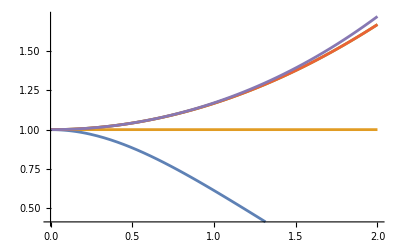

```mathematica
Plot[
{y[x]/.ySolutionN[[1]],
yApprox[1],
yApprox[2],
yApprox[3],
yApprox[4]}
,{x,0,2}]
```

## Saving the data